```mathematica
(*HVEDM AdS case*)
```

1<=z<2 case

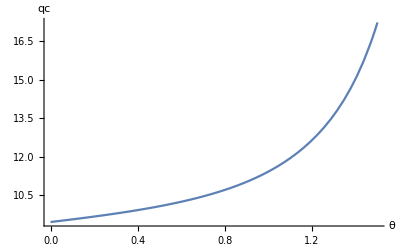

z>2 case

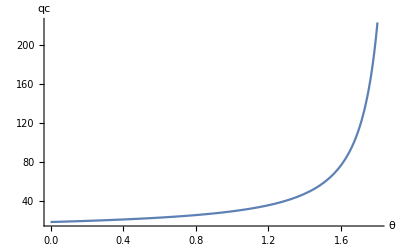

```mathematica
Block[
{qcrit,μextreme},
μextreme[rh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]rh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]];
qcrit[rs_,rh_,μ_,z_,θ_]:=Sqrt[1-(rh/rs)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) rh^(2z-2θ)/rs^(2(z-θ+1))(1-(rh/rs)^(θ-z))]/(μ rs(1-(rh/rs)^(z-θ)));
Print["1<=z<2 case"];
Print[Plot[qcrit[1,0.1,0.75μextreme[0.1,1.75,θ],1.75,θ],{θ,0,1.5},AxesLabel->{θ,qc},AxesOrigin->{0,0},PlotRange->All]];
Print["z>2 case"];
Print[Plot[qcrit[1,0.1,0.75μextreme[0.1,3,θ],3,θ],{θ,0,1.8},AxesLabel->{θ,qc},AxesOrigin->{0,0},PlotRange->All]];
]
```

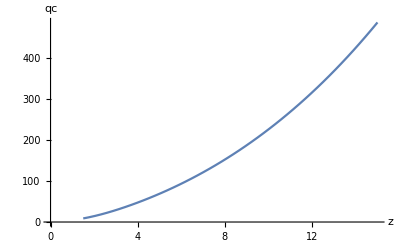

```mathematica
Block[
{qcrit,μextreme},
μextreme[rh_,z_,θ_]:=Sqrt[2(2-θ)(2+z-θ)]rh/(z-θ)Exp[-Sqrt[(z-1+θ/2)/2/(2-θ)]];
qcrit[rs_,rh_,μ_,z_,θ_]:=Sqrt[1-(rh/rs)^(2+z-θ)+μ^2(z-θ)/2/(2-θ) rh^(2z-2θ)/rs^(2(z-θ+1))(1-(rh/rs)^(θ-z))]/(μ rs(1-(rh/rs)^(z-θ)));
Print[Plot[qcrit[1,0.1,0.75μextreme[0.1,z,1],z,1],{z,1.5,15},AxesLabel->{z,qc},AxesOrigin->{0,0}]];
]
```

```mathematica
(* BIAdS plots *)
```

0<=β<=Sqrt[6] case

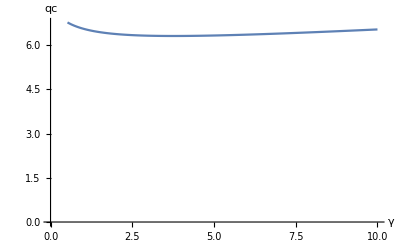

β>Sqrt[6] case

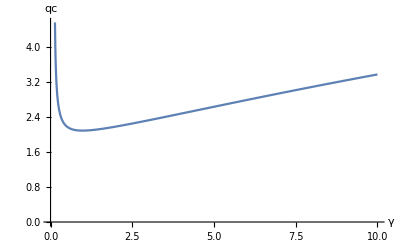

Branch cut 0<=β<=Sqrt[6]

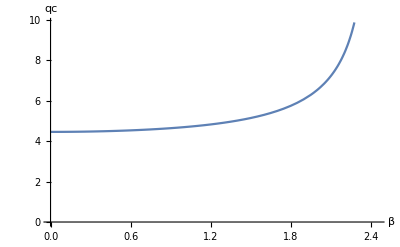

Branch cut β≥ √((2 (1 + 3 γ))/γ)

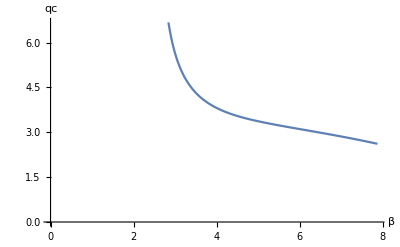

```mathematica
Block[
{m,f,qcrit,μextreme},
m[β_,γ_,μ_]:=-β^2/2+(1-Sqrt[1+γ μ^2])/6/γ+1+μ^2/3Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2];
f[z_,β_,γ_,μ_]:=μ^2 z^4/3 Hypergeometric2F1[1/4,1/2,5/4,-z^4 γ μ^2]+(1-Sqrt[1+γ μ^2 z^4])/6/γ- m [β,γ,μ]z^3+1-β^2 z^2/2;
qcrit[zs_,β_,γ_,μ_]:=Sqrt[f[zs,β,γ,μ]]/zs/(μ*(Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2]-zs Hypergeometric2F1[1/4,1/2,5/4,-γ μ^2 zs^4]));
μextreme[β_,γ_]:=Sqrt[1/γ((1+(6-β^2)γ)^2-1)];
Print["0<=β<=Sqrt[6] case"];
Print[Plot[qcrit[0.1,2,γ,0.75μextreme[2,γ]],{γ,0,10},AxesLabel->{γ,qc},AxesOrigin->{0,0}]];
Print["β>Sqrt[6] case"];
Print[Plot[qcrit[0.1,5,γ,0.75μextreme[5,γ]],{γ,2/(5^2-6),10},AxesLabel->{γ,qc},AxesOrigin->{0,0}]];
Print["Branch cut 0<=β<=Sqrt[6]"];
Print[Plot[qcrit[0.1,β,10,0.75μextreme[β,10]],{β,0,Sqrt[6]},AxesLabel->{β,qc},AxesOrigin->{0,0}]];
Print["Branch cut β≥ √((2 (1 + 3 γ))/γ)"];
Print[Plot[qcrit[0.1,β,10,0.75μextreme[β,10]],{β,Sqrt[2(1+3γ)/γ]/.{γ->10},Sqrt[20(1+3γ)/γ]/.{γ->10}},AxesLabel->{β,qc},AxesOrigin->{0,0}]];
]
```

```mathematica
(* GBAdS plots *)
```

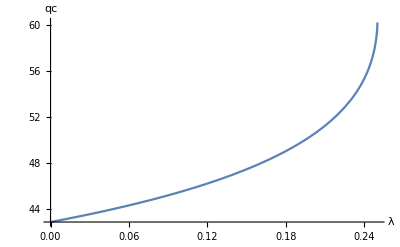

```mathematica
Block[
{μextreme,f,qcrit,m,q},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_]:=Sqrt[8 Pi] rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_]:=Sqrt[f[zs,1/zp,μ,l,λ]]/zs/μ/(1-zs/zp)Sqrt[(1+Sqrt[1-4λ])/2];
μextreme[l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/Sqrt[8 Pi]/l/zh;
Print[Plot[qcrit[0.1,1,0.75μextreme[1,1,λ],1,λ],{λ,0,1/4},AxesLabel->{λ,qc}]];
]
```

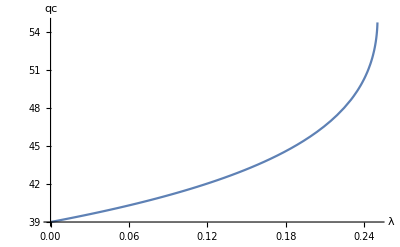

```mathematica
Block[
{μextreme,f,qcrit,m,q},
m[rp_,μ_,l_,λ_]:=rp^4+8Pi l^2μ^2rp^2(1-Sqrt[1-4λ])/3/λ;
q[rp_,μ_,l_,λ_]:=Sqrt[8 Pi] rp^2 l μ Sqrt[(1-Sqrt[1-4λ])/3/λ];
f[z_,rp_,μ_,l_,λ_]:=1/2/λ/l^2(1-Sqrt[1-4λ(1-m[rp,μ,l,λ] z^4+q[rp,μ,l,λ]^2 z^6)]);
qcrit[zs_,zp_,μ_,l_,λ_]:=Sqrt[f[zs,1/zp,μ,l,λ]]/zs/μ/(1-zs^2/zp^2)Sqrt[(1+Sqrt[1-4λ])/2];
μextreme[l_,zh_,λ_]:=Sqrt[3/2(1+Sqrt[1-4λ])]/Sqrt[8 Pi]/l/zh;
Print[Plot[qcrit[0.1,1,0.75μextreme[1,1,λ],1,λ],{λ,0,1/4},AxesLabel->{λ,qc}]];
]
```